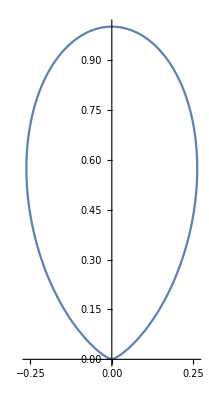

-Graphics3D-

-Graphics3D-

```mathematica
(* 一对正弦发射源，距离是半个波长，相位差为Pi*dd *)
dd  = 0;
h1[x_,t_]:= x Sin[t]; (* 高度 *)
g1[x_,t_] := x Cos[t];(* 投影长度 *)
f1[x_,t_] := Sqrt[h1[x,t]^2 + (g1[x,t]+1)^2] - Sqrt[h1[x,t]^2 + (g1[x,t]-1)^2]; (* 行程差 *)
 f2[x_,t_] := Cos[f1[x,t]*Pi*0.5*0.5+Pi*dd]^2;  (* 叠加后的强度 *)
PolarPlot[f2[500,t],{t,0,Pi}](* 一定距离的波瓣 *) 
ParametricPlot3D[{r*Cos[t],r*Sin[t],100*f2[r,t]},{r,10,1000},{t,0,π}, ColorFunction->Function[{x,y,z,t},Hue[(z+1)/2] ]]
Plot3D[f2[x,t],{x,0,1000},{t,0,Pi}]
```